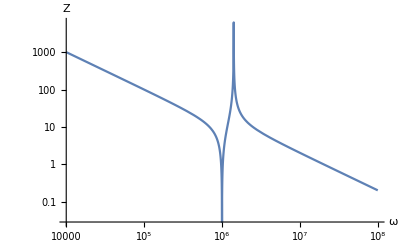

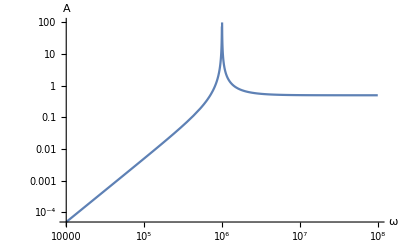

```mathematica
(* Priklad 2*)
ClearAll["Global`*"]
zlr=  r*zl;
zb = 1/(1/zlr+1/zc2);
z = zc1 + zb;
c1 = c2 = 100 *10^-9;
r = 0.1;
l = 50 *10^-6;
zc1 = 1/(ⅉ*ω*c1);
zc2 = 1/(ⅉ*ω*c2);
zl = ⅉ*ω*l;
LogLogPlot[Abs[z], {ω,10^4,10^8}, AxesLabel->{"ω", "Z"}]
 (* Pro prenos *)
LogLogPlot[Abs[zb/(zb+zc1)], {ω,10^4,10^8}, AxesLabel->{"ω", "A"}]
```

```mathematica
(* Priklad 4 *)
ClearAll["Global`*"]
s[a_, b_] := a+b
p[a_, b_] := 1/(1/a+1/b)
za = s [
p[
s[r1,zc1],
s[r2,r3]
],r3]
```

r3+1/(1/(r2+r3)+1/(r1+zc1))

```mathematica
(* Priklad 4 *)
ClearAll["Global`*"]
z = 2000 +300ⅉ;
r = Re[z];
ω = 100;
Solve[Im[z] *ⅉ == ⅉ*ω*l,l];
```

```mathematica
Solve[Im[z]*ⅉ ==  1/(ⅉ*ω*c),c]//N//EngineeringForm
```

{{c→-33.3333×10^-6}}